```mathematica
Module[{a=158.4,b=0.288,c,d,e},NonlinearModelFit[data,Re[{c/(1+Exp[d-Log[a/(b* x)-1/b]/e])}],{{d,2.6},{c,160},{e,0.45}},x]]
```

FittedModel[157.671 Re[1/(1+(2.51409×10^-11)/(-«19»+«1»)^(«19»))]]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.86541 | 0.00671328 | 724.745 | 9.49225×10^-14
x | 0.674422 | 0.12464 | 5.41096 | 0.0029163

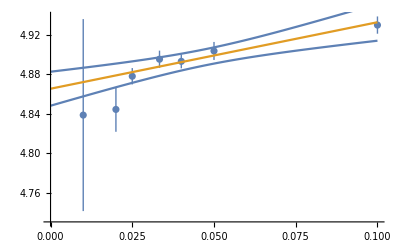

```mathematica
data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};
error=data[[All,2]]/.ErrorBar[x_]->x;
t=Table[{data[[i,1,1]],Around[data[[i,1,2]],error[[i]]]},{i,Length[error]}];
lmf=LinearModelFit[data[[All,1]],x,x,Weights->1/error^2];
lmf["ParameterTable"]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,0.1}]]
```

```mathematica
Import[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/yinsh/Chi8/data/freezeout/fitSTAR

```mathematica
data=Import["stardata.dat"][[All,{2,4,5}]]
```

{{399.8,143.8,2.7},{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5},{69.2,164.3,3.6},{27.,167.8,4.2}}

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

| Estimate | Standard Error | t-Statistic | P-Value
c | 162.217 | 1.55268 | 104.476 | 1.52334×10^-9
e | 0.453047 | 0.0164501 | 27.5407 | 1.18117×10^-6

162.217/(1+13.4637/(-3.47222+4539.93/x)^2.20728)

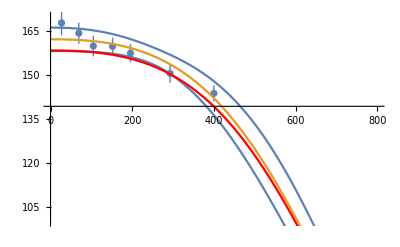

```mathematica
(*data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};*)
error=data[[All,-1]]
t=Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}];
lmf=NonlinearModelFit[data[[All,{1,2}]],c/(1+Exp[2.6-Log[1307.5/(0.288* x)-1/0.288]/e]),{{c,160},{e,1/2}},x,Weights->1/error^2];
lmf["ParameterTable"]
lmf[x]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red],PlotRange->{{0,800},{100,170}}]
```

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

| Estimate | Standard Error | t-Statistic | P-Value
c | 162.217 | 1.55268 | 104.476 | 1.52334×10^-9
e | 0.453047 | 0.0164501 | 27.5407 | 1.18117×10^-6

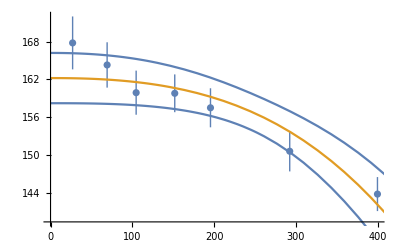

```mathematica
lmf["MeanPredictionBands"]
```

```mathematica
lmf[0.1]
```

162.217

```mathematica
Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}]
```

{{399.8,143.82.7},{292.5,150.63.2},{195.6,157.53.1},{151.9,159.83.0},{104.7,159.93.5},{69.2,164.4.},{27.,168.4.}}

```mathematica
error=data[[All,-1]]
```

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

```mathematica
{lmf["MeanPredictionBands"],lmf[x]}/.x->100
```

{{157.946,165.347},161.646}